```mathematica
rapp[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]/x2[[i,2]]},{i,1,Length[x1]}]
absrapp[x1_,x2_]:=Table[{x1[[i,1]],Abs[x1[[i,2]]/x2[[i,2]]]},{i,1,Length[x1]}]
mult[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]*x2[[i,2]]},{i,1,Length[x1]}]
sum[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]+x2[[i,2]]},{i,1,Length[x1]}]
sumlist[x1_]:=Table[{x1[[1,i,1]],x1[[1,i,2]]+x1[[2,i,2]]+x1[[3,i,2]]},{i,1,Length[x1[[1]]]}]
coeff[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]*c},{i,1,Length[x1]}]
sumconst[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]+c},{i,1,Length[x1]}]
diff[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]-x2[[i,2]]},{i,1,Length[x1]}]
joinbin[x_,n_]:=Map[{(Plus@@#)[[1]]/n,(Plus@@#)[[2]]}&,Partition[x,n]]
```

```mathematica
nomicartelle=Import["/Users/pagani/mg5_3.5/lista_cartellemumumassive.dat","List"]
quantities={aaWW,muaWW,mua,aa,mumu,total,nocutsmuaWW,OPmuaWW,OPmua,OPaa,OPmumu,OPtotal,OPnocutsmuaWW}
```

{aatottformuu,altottl,mupemtomupemtt,mupemtomupemtt_v0,mupemtomupemtt_v2,nocut_mupemtomupemtt,nocuts_altottl,onlyphoton_altottl,onlyphoton_mupemtomupemtt,onlyphoton_mupemtomupemtt_v0,onlyphoton_mupemtomupemtt_v2,onlyphoton_nocut_mupemtomupemtt,onlyphoton_nocuts_altottl}

{aaWW,muaWW,mua,aa,mumu,total,nocutsmuaWW,OPmuaWW,OPmua,OPaa,OPmumu,OPtotal,OPnocutsmuaWW}

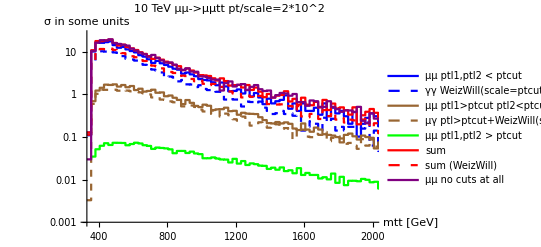

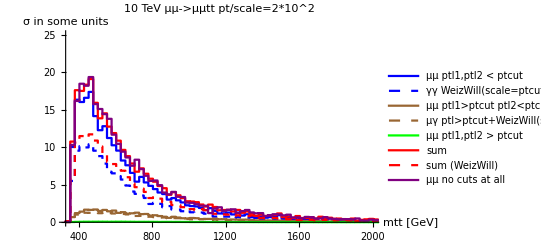

/Users/pagani/mu-vbf/massive_mu/plots/mttplots/logplotmtt10d0.pdf

/Users/pagani/mu-vbf/massive_mu/plots/mttplots/plotmtt10d0.pdf

```mathematica
namerun="distr2ndtry";
ptcutscale=ToString[2];


listaistogrammi=Table[0,{i,1,Length[nomicartelle]}];
Do[
nomi=.;
nhistos=.;
inputname="/Users/pagani/mg5_3.5/"<>nomicartelle[[i]]<>"/HTML/"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/MadAnalysis5job_0/Histograms/histos.saf";

If[i===6 || i===12,inputname="/Users/pagani/mg5_3.5/"<>nomicartelle[[i]]<>"/HTML/"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/tag_2_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/MadAnalysis5job_0/Histograms/histos.saf"];

If[ i===12,inputname="/Users/pagani/mg5_3.5/"<>nomicartelle[[i]]<>"/HTML/"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/MadAnalysis5job_0/Histograms/histos.saf"];


Estrai[inputname,quantities[[i]],nomi,nhistos],
{i,1,Length[nomicartelle]}]
numberplot=11;

unisci[x_]:=joinbin[x,5];

summed=sum[mumu[numberplot],sum[aa[numberplot],mua[numberplot]]];
summedWWa=sum[mumu[numberplot],sum[aaWW[numberplot],muaWW[numberplot]]];
logplotmtt=ListLogPlot[{unisci[aa[numberplot]],unisci[aaWW[numberplot]],unisci[mua[numberplot]],unisci[ muaWW[numberplot]],unisci[mumu[numberplot]],unisci[summed],unisci[summedWWa],unisci[total[numberplot]]},Joined->True,InterpolationOrder->0,AxesLabel->{"mtt [GeV]","σ in some units"},LabelStyle->{FontSize->15},PlotRange->{{330,2000},{10^-3,25}},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ WeizWill(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+WeizWill(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple},PlotLabel->"10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale]]

plotmtt=ListPlot[{unisci[aa[numberplot]],unisci[aaWW[numberplot]],unisci[mua[numberplot]],unisci[ muaWW[numberplot]],unisci[mumu[numberplot]],unisci[summed],unisci[summedWWa],unisci[total[numberplot]]},Joined->True,InterpolationOrder->0,AxesLabel->{"mtt [GeV]","σ in some units"},LabelStyle->{FontSize->15},PlotRange->{{330,2000},{10^-3,25}},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ WeizWill(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+WeizWill(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple},PlotLabel->"10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale]]

Export["/Users/pagani/mu-vbf/massive_mu/plots/mttplots/logplotmtt10d"<>ToString[ptcutscale]<>".pdf",logplotmtt];
Export["/Users/pagani/mu-vbf/massive_mu/plots/mttplots/plotmtt10d"<>ToString[ptcutscale]<>".pdf",plotmtt];

"/Users/pagani/mu-vbf/massive_mu/plots/mttplots/logplotmtt10d0.pdf"
"/Users/pagani/mu-vbf/massive_mu/plots/mttplots/plotmtt10d0.pdf"
```

```mathematica
nomi
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_ETA},{6_PT},{7_ETA},{8_PT},{9_ETA},{10_M},{11_M},{12_M},{13_M},{14_DELTAR},{15_DELTAR},{16_DELTAR}}

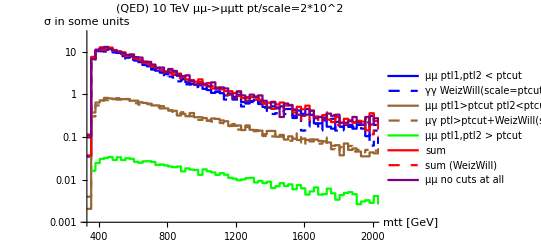

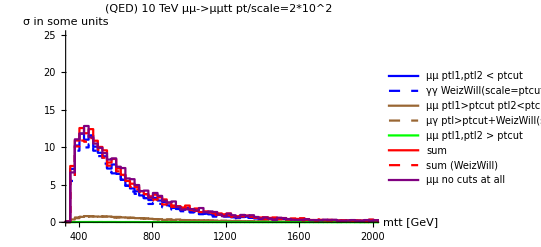

```mathematica
OPsummed=sum[OPmumu[numberplot],sum[OPaa[numberplot],OPmua[numberplot]]];
OPsummedWWa=sum[OPmumu[numberplot],sum[aaWW[numberplot],OPmuaWW[numberplot]]];
OPlogplotmtt=ListLogPlot[{unisci[OPaa[numberplot]],unisci[aaWW[numberplot]],unisci[OPmua[numberplot]],unisci[OPmuaWW[numberplot]],unisci[OPmumu[numberplot]],unisci[OPsummed],unisci[OPsummedWWa],unisci[OPtotal[numberplot]]},Joined->True,InterpolationOrder->0,AxesLabel->{"mtt [GeV]","σ in some units"},LabelStyle->{FontSize->15},PlotRange->{{330,2000},{10^-3,25}},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ WeizWill(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+WeizWill(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple},PlotLabel->"(QED) 10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale]]

OPplotmtt=ListPlot[{unisci[OPaa[numberplot]],unisci[aaWW[numberplot]],unisci[OPmua[numberplot]],unisci[OPmuaWW[numberplot]],unisci[OPmumu[numberplot]],unisci[OPsummed],unisci[OPsummedWWa],unisci[OPtotal[numberplot]]},Joined->True,InterpolationOrder->0,AxesLabel->{"mtt [GeV]","σ in some units"},LabelStyle->{FontSize->15},PlotRange->{{330,2000},{10^-3,25}},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ WeizWill(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+WeizWill(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple},PlotLabel->"(QED) 10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale]]
```

```mathematica
Export["/Users/pagani/mu-vbf/massive_mu/plots/mttplots/OPlogplotmtt10d"<>ToString[ptcutscale]<>".pdf",OPlogplotmtt];
Export["/Users/pagani/mu-vbf/massive_mu/plots/mttplots/OPplotmtt10d"<>ToString[ptcutscale]<>".pdf",OPplotmtt];
```